```mathematica
yixia@home Aug 21,2010  model fit for netlogo modeling
```

```mathematica
data={{0,183},{1,32},{2,21},{3,9}, {4,7},{5,6},{6,1}};
```

```mathematica
nlm=NonlinearModelFit[data,β(x+1)^(-γ),{β,γ},x]
nlm[{"ParameterTable","RSquared"}]
```

FittedModel[182.52/(1+x)^(«19»)]

{ | Estimate | Standard Error | t Statistic | P-Value
β | 182.52 | 4.1271 | 44.2246 | 1.11585×10^-7
γ | 2.28299 | 0.124305 | 18.3661 | 8.8009×10^-6,0.997566}

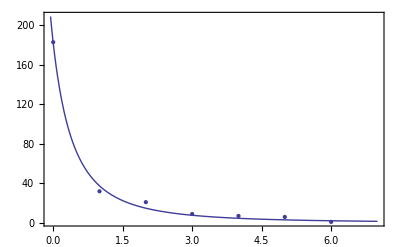

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,-1,7}],Frame->True]
```

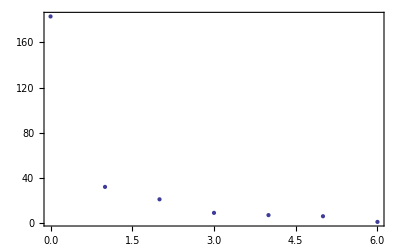

```mathematica
Show[ListPlot[data],Frame->True]
```

```mathematica
Normal[nlm]
```

182.52/(1+x)^2.28299

```mathematica
nlm=NonlinearModelFit[data,β-γ*ln(x+1),{β,γ},x]
```

NonlinearModelFit[{{0,183},{1,32},{2,21},{3,9},{4,7},{5,6},{6,1}},β-ln (1+x) γ,{β,γ},x]

```mathematica
y=f(X)=182.5197664326006/(1+x)^2.2829889871175135
```

182.52/(1+x)^2.28299

```mathematica
y=f(x)=β(x+1)^(-γ)
```

```mathematica
f(x)=β*(1+x)^-γ
```